```mathematica
a={1,3,1};
T = .2;
A = {{0,1,0},{0,0,1},-a};
F[T_,idx_]:=Sum[(MatrixPower[A,j]*(T^j))/(j!),{j,0,idx}];
parallelF[T_,idx_]:=ParallelSum[(MatrixPower[A,j]*(T^j))/(j!),{j,0,idx}];
Period = 8;
Kh = Period/T;

x0 = {{-1,0,0}};

x1 = x2 = x3 = x0;

F1t=F[T,1];
F2t=F[T,2];
F3t=F[T,3];

For[k=1,k ≤  Kh,k++,{x1= Append[x1,F1t.x1[[k]]] ,x2= Append[x2,F2t.x2[[k]]],x3= Append[x3,F3t.x3[[k]]]}];

t = Range[Kh+1];

x1t = Transpose[Prepend[{x1[[All,1]]},t]];
x2t = Transpose[Prepend[{x2[[All,1]]},t]];
x3t = Transpose[Prepend[{x3[[All,1]]},t]];

ListLinePlot[{x1t,x2t,x3t},ImageSize->Large,PlotMarkers->{"○", "□", "◇"},PlotLegends->{"x1,k","x2,k","x3,k"},Filling->{1->{3}},FillingStyle->Accumulate]
```

-Graphics-

```mathematica
Nh = 3*Kh;

P[M_,X0_,T_]:=(X=X0;For[k=1,k≤Nh,k++,{X=Append[X,M.X[[k]]]}];X);

x1 = P[F1t,x0 ,T];
x2 = P[F2t,x0 ,T];
x3 = P[F3t,x0 ,T];

t = Range[Nh+1];

x1t = Transpose[Prepend[{x1[[All,1]]},t]];
x2t = Transpose[Prepend[{x2[[All,1]]},t]];
x3t = Transpose[Prepend[{x3[[All,1]]},t]];

ListLinePlot[{x1t,x2t,x3t},ImageSize->Large,PlotMarkers->{"○", "□", "◇"},PlotRange->Full,PlotLegends->{"P[F[T,1],x0 ,T].x1,k","P[F[T,2],x0 ,T].x1,k","P[F[T,3],x0 ,T].x1,k"},Filling->{1->{3}}]
```

-Graphics-

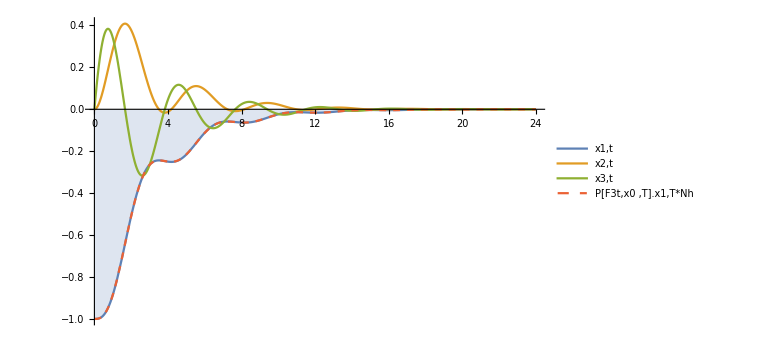

```mathematica
Xvars[tv_]={x1v[tv],x2v[tv],x3v[tv]};
system=Join[Xvars'[tv],Xvars[0]]  == Join[A.Xvars[tv],x0[[1]]];

sol=NDSolve[system,{x1v,x2v,x3v},{tv,0,T*Nh}];

X1interpFunc=sol[[All,1]][[1,2]];
X2interpFunc=sol[[All,2]][[1,2]];
X3interpFunc=sol[[All,3]][[1,2]];

x1d = P[F3t,x0 ,T];

range = Range[0,T*Nh,T];

x1t = Transpose[Prepend[{x1d[[All,1]]},range]];

x1dInterpFunc = Interpolation[x1t];

Plot[{X1interpFunc[t],X2interpFunc[t],X3interpFunc[t],x1dInterpFunc[t]},{t,0,T*Nh},ImageSize->Large, PlotRange->All, PlotLegends->{"x1,t","x2,t","x3,t","P[F[T,3],x0 ,T].x1,T*Nh"},PlotStyle->{Automatic,Automatic,Automatic,Dashed},Filling->{1-> Axis}]
```